```mathematica
eq1=x^2+y^2==4
eq2=Sin[2 x]+Cos[3 y]==1
eq3=0≤x≤Pi
eq4=0≤y≤Pi
```

x^2+y^2==4

Cos[3 y]+Sin[2 x]==1

0≤x≤π

0≤y≤π

```mathematica
N[Solve[{eq1,eq2,0⩽x⩽Pi,0⩽y⩽Pi},{x,y}]]
```

{{x→0.0199619,y→1.9999},{x→1.13234,y→1.64858}}

```mathematica
ans1=NSolve[{eq1,eq2,eq3,eq4},{x,y}]
```

{{x→0.0199619,y→1.9999},{x→1.13234,y→1.64858}}

```mathematica
fig1=ContourPlot[{x^2+y^2==4,Sin[2 x]+Cos[3 y]==1},{x,0,Pi},{y,0,Pi}];
```

```mathematica
fig2=ListPlot[{{x/.ans1[[1]],y/.ans1[[1]]},{x/.ans1[[2]],y/.ans1[[2]]}},PlotStyle->(Red)];
```

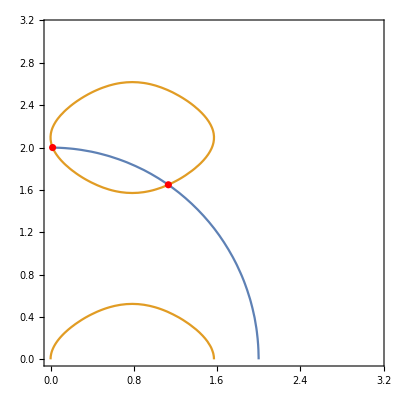

```mathematica
Show[fig1,fig2]
```